PIEZOMETER

```mathematica
Manipulate[
Module[{Patm,g,ρ,H1,H2,δx,th,r0,δw,γ,h,z1},
Patm=1013;(*mbar*)g=9.8;(*m/s/s*)ρ=1000;(*kg/m3*)

(*If[fluid==3,
{H1=1.5;H2=5;δx=1.5;th=0.25;r0=1.;δw=2*th;},
{H1=3;H2=9;δx=2;th=0.5;r0=1.5;δw=2*th;}];*)
H1=3;H2=9;δx=2;th=0.5;r0=1.5;δw=2*th;

γ[1]=Switch[fluid,1,1,2,0.88,3,13.6]*ρ*g;
h[1]=(*If[fluid==3,4,1]**)If[fluid==3,th,0]+(h1/.Quiet@Solve[100*(P1-Patm)==γ[1]*h1/100,h1][[1]]);
z1=Rescale[P1,{1020,1014}];

Show[
Graphics3D[{CapForm@"Butt",
{Opacity@0.5,
Cylinder[{{-δx-r0,0,-δx/2},{-δx-r0,0,H1}},r0],Cylinder[{{-δx-r0,0,H1+0.5*r0},{-δx-r0,0,H1+0.75*r0}},0.167*r0],
Tube[{{0,0,h[1]},{0,0,H2}},th]},
{Switch[fluid,1,RGBColor[0,0.6,1],2,RGBColor[0,0.85,0],3,Orange],
Tube[{{-δx,0,0},{0,0,0},{0,0,h[1]}},th],Cylinder[{{-δx-r0,0,-δx/2},{-δx-r0,0,δx/2+0.15*z1*H1}},r0]},

Text[Style[Subscript[Style["P",Italic],"g"],18],{-δx-r0,0,H1+2*r0},{0,-1.5}],
Arrow[{{-δx-r0,0,H1+2*r0},{-δx-r0,0,H1+0.75*r0}}],
Text[Style[Subscript[Style["P",Italic],"atm"],18],{0,0,1.05*H2}],

Line[{{δw,0,-th},{δw,0,h[1]}}],Line[{{0.7*δw,0,#},{1.3*δw,0,#}}]&/@{-th,h[1]},
Text[Style[Subscript[Style["h",Italic],1],18,Background->White],{δw,0,(h[1]-th)/2}],

Text[Style[Column[{
Row@{Subscript[Style["h",Italic],1]," = ",NumberForm[h[1],{3,1}]," cm"},
Row@{"Δ",Style["P",Italic]," = ",Subscript[Style["P",Italic],"g"]," - ",Subscript[Style["P",Italic],"atm"]," = ",P1-Patm," mbar"}
},Center],18],{δw,0,(H2-th)/2},{-1.5,0}],

(*If[fluid==3,Text[Style["⋆scale is smaller⋆",16],{0,0,-δx/2},{0,-1}]]*)
}],
ParametricPlot3D[{r0*Cos[ϕ]*Sin[θ]-δx-r0,r0*Sin[θ]*Sin[ϕ],0.5*r0*Cos[θ]+H1},{ϕ,-π,π},{θ,0,π/2},Mesh->None,PlotStyle->Opacity[0.5,White],BoundaryStyle->Black],
Boxed->False,ViewPoint->Front,ImageSize->{600,425}]
],
Grid[{
{Control[{{fluid,3,"gage fluid"},{1->" water ",2->" oil ",3->" mercury "},Setter}],SpanFromLeft,
Control[{{SM,1,""},{1->" piezometer ",2->" simple U-tube ",3->" inclined "},Setter}]},
{Row@{"gage fluid pressure ",Subscript[Style["P",Italic],"g"]," (mbar)"},
Control[{{P1,1020,""},1014,1020,1,Appearance->"Labeled"}],SpanFromLeft}
},Alignment->Left]
]
```

U-TUBE MANOMETER

```mathematica
Manipulate[
Module[{Patm,g,ρ,H1,δx,th,r0,δw,γ,h},
Patm=1013;(*mbar*)g=9.8;(*m/s/s*)ρ=1000;(*kg/m3*)

H1=8.5;δx=2;th=0.5;r0=1.5;δw=2*th;
γ[2]=Switch[fluid,1,1,2,0.88,3,13.6]*ρ*g;
h[2]=0.5*H1*(1+Rescale[h2/.Quiet@Solve[100*(P2-Patm)==γ[2]*h2/100,h2][[1]],{0,8.5}]);
h[1]=H1-h[2];

Graphics3D[{CapForm@"Butt",
{Opacity@0.5,Tube[{{-δx-r0,0,H1},{-δx,0,H1},{-δx,0,h[1]}},th],Tube[{{δx,0,h[2]},{δx,0,H1}},th],Sphere[{-δx-1.95*r0,0,H1},r0]},
{Switch[fluid,1,RGBColor[0,0.6,1],2,RGBColor[0,0.85,0],3,Orange],Tube[{{-δx,0,h[1]},{-δx,0,0},{δx,0,0},{δx,0,h[2]}},th]},

Line[{{-δx+δw,-th,H1+th/2},{-δx+δw,-th,h[1]}}],Line[{{-δx+0.7*δw,-th,#},{-δx+1.3*δw,-th,#}}]&/@{H1+th/2,h[1]},
Text[Style[Subscript[Style["h",Italic],1],18,Background->White],{-δx+δw,-th,(H1+th/2+h[1])/2}],

Line[{{δx+δw,0,h[1]},{δx+δw,0,h[2]}}],Line[{{δx+0.7*δw,0,#},{δx+1.3*δw,0,#}}]&/@{h[1],h[2]},
Text[Style[Subscript[Style["h",Italic],2],18,Background->White],{δx+δw,0,(h[1]+h[2])/2},{If[2*(h[2]-H1/2)<1,-2.5,0],0}],

Text[Style[Subscript[Style["P",Italic],#1],20],#2]&@@@{{"g",{-δx-2*r0,0,H1}},{"atm",{δx,0,1.1*H1}}},

Text[Style[Column[{
Row@{Subscript[Style["h",Italic],1]," = ",NumberForm[H1-h[1],{3,1}]," cm"},
Row@{Subscript[Style["h",Italic],2]," = ",NumberForm[2*(h[2]-H1/2),{3,1}]," cm"},
Row@{"Δ",Style["P",Italic]," = ",Subscript[Style["P",Italic],"g"]," - ",Subscript[Style["P",Italic],"atm"]," = ",P2-Patm," mbar"}
},Center],18],{8,0,6}]
},Boxed->False,ViewPoint->Front,ImageSize->{600,425}]
],
Grid[{
{Control[{{fluid,1,"gage fluid"},{1->" water ",2->" oil ",3->" mercury "},Setter}],SpanFromLeft,
Control[{{SM,1,""},{1->" piezometer ",2->" simple U-tube ",3->" inclined "},Setter}]},
{Row@{"gage fluid pressure ",Subscript[Style["P",Italic],"g"]," (mbar)"},
Control[{{P2,1020,""},1013,1020,1,Appearance->"Labeled"}],SpanFromLeft}
},Alignment->Left]
]
```

INCLINED MANOMETER

```mathematica
Manipulate[
Module[{Patm,g,ρ,δx,th,δw,H,r0,γ,h,L,y0,x0,data},
Patm=1013;(*mbar*)g=9.8;(*m/s/s*)ρ=1000;(*kg/m3*)

δx=2;th=1.5;δw=1.75*th;H=10;r0=8;L[0]=If[fluid==3,25,80];
γ[2]=Switch[fluid,1,1,2,0.8,3,13.6(*1.88*)]*ρ*g;
h[2]=h2/.Quiet@Solve[100*(P3-Patm)==γ[2]*h2/100,h2][[1]];
L[2]=h[2]*Csc[θ];
h[1]=Rescale[P3,{1014,1025}];
y0[1]=0.5*(H-h[1]-δx);x0[1]=y0[1]*Cot[θ];L[1]=y0[1]*Csc[θ];
y0[2]=y0[1]+h[2];x0[2]=x0[1]+L[2]*Cos[θ];
L[3]=L[0]-L[1]-L[2];
y0[3]=y0[2]+L[3]*Sin[θ];x0[3]=x0[2]+L[3]*Cos[θ];

(*data={{0.2617993877991494,7.7},{0.26354471705114374,7.66},{0.26529004630313807,7.62},{0.2670353755551324,7.58},{0.26878070480712674,7.54},{0.27052603405912107,7.5},{0.2722713633111154,7.46},{0.27401669256310973,7.42},{0.27576202181510406,7.38},{0.2775073510670984,7.34},{0.2792526803190927,7.3},{0.280998009571087,7.260000000000001},{0.28274333882308134,7.220000000000001},{0.28448866807507567,7.180000000000001},{0.28623399732707,7.140000000000001},{0.28797932657906433,7.1000000000000005},{0.28972465583105866,7.0600000000000005},{0.291469985083053,7.0200000000000005},{0.29321531433504733,6.98},{0.29496064358704166,6.94},{0.296705972839036,6.9},{0.2984513020910303,6.86},{0.30019663134302466,6.82},{0.301941960595019,6.78},{0.3036872898470133,6.74},{0.30543261909900765,6.7},{0.307177948351002,6.66},{0.3089232776029963,6.62},{0.31066860685499065,6.58},{0.312413936106985,6.54},{0.3141592653589793,6.5},{0.31590459461097364,6.46},{0.317649923862968,6.42},{0.3193952531149623,6.38},{0.32114058236695664,6.34},{0.32288591161895097,6.3},{0.3246312408709453,6.26},{0.32637657012293964,6.22},{0.3281218993749339,6.180000000000001},{0.32986722862692824,6.140000000000001},{0.3316125578789226,6.1000000000000005},{0.3333578871309169,6.0600000000000005},{0.33510321638291124,6.0200000000000005},{0.33684854563490557,5.98},{0.3385938748868999,5.94},{0.34033920413889424,5.9},{0.34208453339088857,5.86},{0.3438298626428829,5.82},{0.34557519189487723,5.78},{0.34732052114687156,5.74},{0.3490658503988659,5.7}};*)

data=Quiet@Interpolation[{{0.2617,7.7},{0.3491,5.7}}][θ];

Show[
Graphics3D[{CapForm@"Butt",
{Opacity@0.5,Cylinder[{{-δx-r0,0,y0[1]},{-δx-r0,0,H}},r0],Cylinder[{{-δx-r0,0,H+0.5*r0},{-δx-r0,0,1.2*H+0.5*r0}},0.2*r0]},
{Switch[fluid,1,RGBColor[0,0.6,1],2,RGBColor[0,0.85,0],3,Orange],Style[
Tube[{{-δx,0,0},{0,0,0},{x0[3],0,y0[3]}},th],
ClipPlanes->InfinitePlane[{{0,0,y0[2]},{1,0,y0[2]},{0,-1,y0[2]}}]],
Cylinder[{{-δx-r0,0,-δx},{-δx-r0,0,y0[1]}},r0]},
{Opacity@0.5,Style[
Tube[{{0,0,0},{x0[3],0,y0[3]}},th],
ClipPlanes->InfinitePlane[{{0,0,y0[2]},{1,0,y0[2]},{0,1,y0[2]}}]]},

Arrowheads@0.03,Arrow[{{-δx-r0,0,1.8*H+0.5*r0},{-δx-r0,0,1.2*H+0.5*r0}}],
Text[Style[Subscript[Style["P",Italic],#1],18],#2,{0,-1.5}]&@@@{{"g",{-δx-r0,0,1.8*H+0.5*r0}},{"atm",{x0[3],0,y0[3]+th}}},

{Dashed,Line[{{-δx,-th,y0[1]},{x0[2]+3*th,-th,y0[1]}}]},

Line[{{x0[2]+3*th,-th,y0[1]},{x0[2]+3*th,-th,y0[2]}}],Line[{{x0[2]+3*th-0.3*δw,-th,#},{x0[2]+3*th+0.3*δw,-th,#}}]&/@{y0[1],y0[2]},
Text[Style[Subscript[Style["h",Italic],1],18,Background->White],{x0[2]+3*th,-th,(y0[1]+y0[2])/2},{If[h[2]<2.6,-2,0],0}],

(*Line[{{x0[1]-2*1.5*th,-th,y0[1]+1.5*th},{x0[2]-2*1.5*th,-th,y0[2]+1.5*th}}],*)
Text[Style[Subscript[Style["L",Italic],1],18,Background->White],{(x0[1]+x0[2])/2-2*1.5*th,-th,(y0[1]+y0[2])/2+1.5*th},{0,If[L[2]<5,-1.5,0]}],
(*Text[Rotate[Style["—",17],90°+θ],#]&/@{{x0[1]-2*1.5*th,0,y0[1]+1.5*th},{x0[2]-2*1.5*th,0,y0[2]+1.5*th}},*)
(*Text[Rotate[Style["—",17],90°+θ],#]&/@{{x0[1],0,y0[1]},{x0[2],0,y0[2]}},*)
(*Text[Rotate[Style["—",17],90°+θ],#]&/@{(*{x0[1]-2*1.5*th,0,y0[1]+1.5*th}*)
{data,0,y0[1]+th},{x0[2]-2*1.5*th,0,y0[2]+1.5*th}},*)
Line[{{data,-th,y0[1]},{x0[1]+h[2]*Csc[θ],-th,y0[2]}}],
(*Text[Rotate[Style["—",17],90°+θ],#]&/@{{data,0,y0[1]+th},{x0[2]*Csc[θ],0,y0[2]+th}},*)

Line[{{0,0,-th},{7,0,-th}}],Text[Style["θ",18,Italic],{7,0,-th},{-1,-0.5}],

Text[Style[Column[{
Row@{Subscript[Style["h",Italic],1]," = ",NumberForm[h[2],{3,1}]," cm",Spacer@10,
Subscript[Style["L",Italic],1]," = ",NumberForm[L[2],{3,1}]," cm"},
Row@{"Δ",Style["P",Italic]," = ",Subscript[Style["P",Italic],"g"]," - ",Subscript[Style["P",Italic],"atm"]," = ",P3-Patm," mbar"},
Row@{Style["θ",Italic]," = ",NumberForm[N@θ*180/π,{3,1}],"°"}
},Center],18],{L[0]/3,0,If[fluid==3,20,35](*2*H+0.5*r0*)(*1.3*L[0]*Sin[20°]*)}],

Point[{pt,0,y0[1]}],Text[Style[pt,17],{pt,0,y0[1]},{0,-1.5}]
}],
ParametricPlot3D[{r0*Cos[ϕ]*Sin[θ]-δx-r0,r0*Sin[θ]*Sin[ϕ],0.5*r0*Cos[θ]+H},{ϕ,-π,π},{θ,0,π/2},Mesh->None,PlotStyle->Opacity[0.5,White],BoundaryStyle->Black],
Boxed->False,ViewPoint->Front,ImageSize->{600,425},PlotRange->{{-δx-2*r0,L[0]},All,{-1.02*δx,If[fluid==3,1.8*H+0.5*r0,L[0]*Sin[20°]]}}]
(*Quiet@Interpolation[{{0.2617,7.7},{0.3491,5.7}}][θ]*)

],
Grid[{
{Control[{{fluid,3,"gage fluid"},{1->" water ",2->" oil ",3->" mercury "},Setter}],SpanFromLeft,
Control[{{SM,1,""},{1->" piezometer ",2->" simple U-tube ",3->" inclined "},Setter}]},
{Row@{"gage fluid pressure ",Subscript[Style["P",Italic],"g"]," (mbar)"},
Grid@{{
Control[{{P3,1020,""},1014,1025,1,Appearance->"Labeled",ImageSize->Small}],
Row@{Control[{{θ,15°,"angle"},15°,20°,0.1°,ImageSize->Small}],Spacer@5,N@Dynamic[θ*180/π],"°"}
}},SpanFromLeft}
},Alignment->Left],
Control[{{pt,0},0,10,0.1,Appearance->"Labeled"}]
]
```

```mathematica
1/Sin[th]
```

Csc[th]

```mathematica
Manipulate[
Interpolation[{{15°,7.7},{20°,5.7}}][θ],
Row@{Control[{{θ,15°,"angle"},15°,20°,1°,ImageSize->Small}],Spacer@5,N@Dynamic[θ*180/π],"°"}]
```

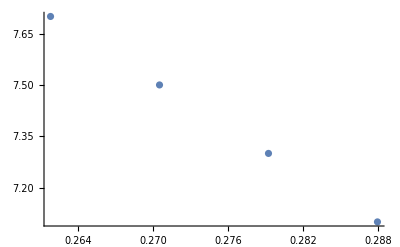

```mathematica
ListPlot@{{15°,7.7},{15.5°,7.5},{16°,7.3},{16.5°,7.1}}
```

```mathematica
{#,Quiet@Interpolation[{{15°,7.7},{15.5°,7.5},{16°,7.3},{16.5°,7.1}}][#]}&/@Range[15°,20°,1°]
```

{{15 °,7.7},{16 °,7.3},{17 °,6.9},{18 °,6.5},{19 °,6.1},{20 °,5.7}}

```mathematica
{{15 °,7.7},{16 °,7.3},{17 °,6.9},{18 °,6.5},{19 °,6.1},{20 °,5.7}}
```

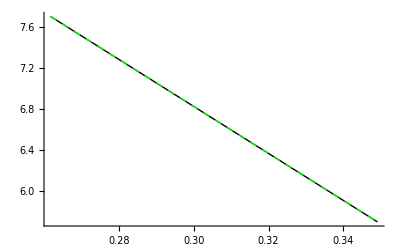

```mathematica
Show[
ListPlot[{{15 °,7.7},{16 °,7.3},{17 °,6.9},{18 °,6.5},{19 °,6.1},{20 °,5.7}},Joined->True,PlotStyle->{Thick,Black}],
ListPlot[{{15°,7.7},{20°,5.7}},Joined->True,PlotStyle->{Thick,Dashed,Green}]
]
```

```mathematica
{#,Quiet@Interpolation[{{15°,7.7},{20°,5.7}}][#]}&/@Range[15°,20°,0.1°]
```

{{0.261799,7.7},{0.263545,7.66},{0.26529,7.62},{0.267035,7.58},{0.268781,7.54},{0.270526,7.5},{0.272271,7.46},{0.274017,7.42},{0.275762,7.38},{0.277507,7.34},{0.279253,7.3},{0.280998,7.26},{0.282743,7.22},{0.284489,7.18},{0.286234,7.14},{0.287979,7.1},{0.289725,7.06},{0.29147,7.02},{0.293215,6.98},{0.294961,6.94},{0.296706,6.9},{0.298451,6.86},{0.300197,6.82},{0.301942,6.78},{0.303687,6.74},{0.305433,6.7},{0.307178,6.66},{0.308923,6.62},{0.310669,6.58},{0.312414,6.54},{0.314159,6.5},{0.315905,6.46},{0.31765,6.42},{0.319395,6.38},{0.321141,6.34},{0.322886,6.3},{0.324631,6.26},{0.326377,6.22},{0.328122,6.18},{0.329867,6.14},{0.331613,6.1},{0.333358,6.06},{0.335103,6.02},{0.336849,5.98},{0.338594,5.94},{0.340339,5.9},{0.342085,5.86},{0.34383,5.82},{0.345575,5.78},{0.347321,5.74},{0.349066,5.7}}

```mathematica
Manipulate[
(*Interpolation[{{0.2617993877991494,7.7},{0.27052603405912107,7.5},{0.2792526803190927,7.3},{0.28797932657906433,7.1000000000000005},{0.296705972839036,6.9},{0.30543261909900765,6.7},{0.3141592653589793,6.5},{0.32288591161895097,6.3},{0.3316125578789226,6.1000000000000005},{0.34033920413889424,5.9},{0.3490658503988659,5.7}}][θ],*)
Interpolation[{{0.2617,7.7},{0.2705,7.5},{0.2793,7.3},{0.288,7.1},{0.2967,6.9},{0.3054,6.7},{0.3142,6.5},{0.3229,6.3},{0.3316,6.1},{0.3403,5.9},{0.3491,5.7}}][θ],
Control[{{θ,15°,"angle"},15°,20°,1°,ImageSize->Small}]
]
```

```mathematica
Round[{{0.2617993877991494,7.7},{0.27052603405912107,7.5},{0.2792526803190927,7.3},{0.28797932657906433,7.1000000000000005},{0.296705972839036,6.9},{0.30543261909900765,6.7},{0.3141592653589793,6.5},{0.32288591161895097,6.3},{0.3316125578789226,6.1000000000000005},{0.34033920413889424,5.9},{0.3490658503988659,5.7}},0.0001]
```

{{0.2618,7.7},{0.2705,7.5},{0.2793,7.3},{0.288,7.1},{0.2967,6.9},{0.3054,6.7},{0.3142,6.5},{0.3229,6.3},{0.3316,6.1},{0.3403,5.9},{0.3491,5.7}}

```mathematica
Module[{data},
data={{0.2617993877991494,7.7},{0.26354471705114374,7.66},{0.26529004630313807,7.62},{0.2670353755551324,7.58},{0.26878070480712674,7.54},{0.27052603405912107,7.5},{0.2722713633111154,7.46},{0.27401669256310973,7.42},{0.27576202181510406,7.38},{0.2775073510670984,7.34},{0.2792526803190927,7.3},{0.280998009571087,7.260000000000001},{0.28274333882308134,7.220000000000001},{0.28448866807507567,7.180000000000001},{0.28623399732707,7.140000000000001},{0.28797932657906433,7.1000000000000005},{0.28972465583105866,7.0600000000000005},{0.291469985083053,7.0200000000000005},{0.29321531433504733,6.98},{0.29496064358704166,6.94},{0.296705972839036,6.9},{0.2984513020910303,6.86},{0.30019663134302466,6.82},{0.301941960595019,6.78},{0.3036872898470133,6.74},{0.30543261909900765,6.7},{0.307177948351002,6.66},{0.3089232776029963,6.62},{0.31066860685499065,6.58},{0.312413936106985,6.54},{0.3141592653589793,6.5},{0.31590459461097364,6.46},{0.317649923862968,6.42},{0.3193952531149623,6.38},{0.32114058236695664,6.34},{0.32288591161895097,6.3},{0.3246312408709453,6.26},{0.32637657012293964,6.22},{0.3281218993749339,6.180000000000001},{0.32986722862692824,6.140000000000001},{0.3316125578789226,6.1000000000000005},{0.3333578871309169,6.0600000000000005},{0.33510321638291124,6.0200000000000005},{0.33684854563490557,5.98},{0.3385938748868999,5.94},{0.34033920413889424,5.9},{0.34208453339088857,5.86},{0.3438298626428829,5.82},{0.34557519189487723,5.78},{0.34732052114687156,5.74},{0.3490658503988659,5.7}};

Position[data,15.1°]
]
```

{{2,1}}